```mathematica
Needs["Graphics`Graphics3D`"]
```

Get::noopen: Cannot open Graphics`Graphics3D`.

Needs::nocont: Context Graphics`Graphics3D` was not created when Needs was evaluated.

$Failed

```mathematica
Clear[ψ1slit,ρ1slit,x,t,k,k,a,s,u,v,t1];
```

```mathematica
Clear[w,ρ2slits,solution,a,n0,D1,L,k,s,x,t,slope,slope0,S1,G1,K1,K2,c1,b1];
```

```mathematica
Clear[a,x,s,t,b,c1,PS,S1,Ref1,Imf1,X0,C1,c1,S1];
```

```mathematica
ψ1slit[x_,t_,a_,k_]:=(ⅇ^(-(ⅈ k^2 t+2 ⅈ √2 a k (-x)+x^2)/(4 a^2+2 ⅈ t)) (2/π)^(1/4))/(√a √(2+(ⅈ t)/a^2));
ρ1slit[x_,t_,a_,k_]:=(a ⅇ^(-Re[(k t+√2 a (-x))^2/(4 a^4+t^2)]) √(2/π))/(√(4 a^4+t^2));
```

```mathematica
Simplify[ⅈ/2 D[ψ1slit[x,t,a,k], {x,2}]-D[ψ1slit[x,t,a,k], {t,1}]]
```

0

```mathematica
a=1.0;  s=1.0;b=.1;  k=0;  (* Repeat Below  *)
```

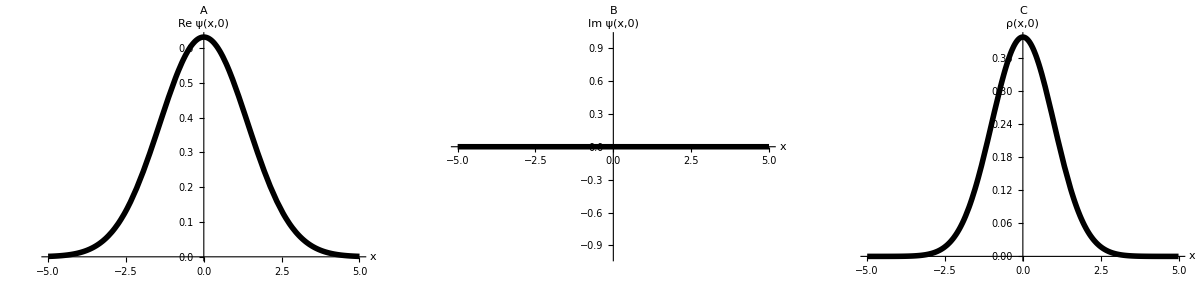

```mathematica
WA=Plot[Re[ψ1slit[x,0,a,k]],{x,-5,5},AspectRatio->.7,PlotRange->All,AxesLabel->{"x","Re ψ(x,0)"},PlotStyle->{Black,Thickness[.01]},PlotLabel->"A"];
WB=Plot[Im[ψ1slit[x,0,a,k]],{x,-5,5},AspectRatio->.7,PlotRange->All,AxesLabel->{"x","Im ψ(x,0)"},PlotStyle->{Black,Thickness[.01]},PlotLabel->"B"];
WC=Plot[ρ1slit[x,0,a,k],{x,-5,5},AspectRatio->.7,PlotRange->All,AxesLabel->{"x","ρ(x,0)"},PlotStyle->{Black,Thickness[.01]},PlotLabel->"C"];
GraphicsRow[{WA,WB,WC},Frame->True]
```

```mathematica
∫_-10^10 ρ1slit[x,0,a,k]ⅆx//N
```

1.

```mathematica
Clear[a,b,s,k]
```

```mathematica
ComplexExpand[ψ1slit[x,0,a,k]]
```

(ⅇ^(-x^2/(4 a^2)) Cos[(k x)/(√2 a)] Cos[Arg[a]/2])/((a^2)^(1/4) (2 π)^(1/4))+(ⅇ^(-x^2/(4 a^2)) Sin[(k x)/(√2 a)] Sin[Arg[a]/2])/((a^2)^(1/4) (2 π)^(1/4))+ⅈ ((ⅇ^(-x^2/(4 a^2)) Cos[Arg[a]/2] Sin[(k x)/(√2 a)])/((a^2)^(1/4) (2 π)^(1/4))-(ⅇ^(-x^2/(4 a^2)) Cos[(k x)/(√2 a)] Sin[Arg[a]/2])/((a^2)^(1/4) (2 π)^(1/4)))

```mathematica
Ref[x_]:=((a^2)^(3/4) ⅇ^(-x^2/(4 a^2)) Cos[(k x)/(√2 a)] Cos[Arg[a]/2])/(a^2 (2 π)^(1/4))+((a^2)^(3/4) ⅇ^(-x^2/(4 a^2)) Sin[(k x)/(√2 a)] Sin[Arg[a]/2])/(a^2 (2 π)^(1/4));
Imf[x_]:=((a^2)^(3/4) ⅇ^(-x^2/(4 a^2)) Cos[Arg[a]/2] Sin[(k x)/(√2 a)])/(a^2 (2 π)^(1/4))-((a^2)^(3/4) ⅇ^(-x^2/(4 a^2)) Cos[(k x)/(√2 a)] Sin[Arg[a]/2])/(a^2 (2 π)^(1/4));
```

```mathematica
Simplify[Ref[x]]
```

(ⅇ^(-x^2/(4 a^2)) Cos[(k x)/(√2 a)-Arg[a]/2])/((a^2)^(1/4) (2 π)^(1/4))

```mathematica
Simplify[Imf[x]]
```

(ⅇ^(-x^2/(4 a^2)) Sin[(k x)/(√2 a)-Arg[a]/2])/((a^2)^(1/4) (2 π)^(1/4))

```mathematica
c1[a_,b_,s_,k_]:=1/√(∫_(-s-b)^(-s+b) Ref[x]^2 ⅆx+∫_(-s-b)^(-s+b) Imf[x]^2 ⅆx+∫_(s-b)^(s+b) Ref[x]^2 ⅆx+∫_(s-b)^(s+b) Imf[x]^2 ⅆx);
```

```mathematica
a=1.0;  s=1.0;b=.1;  k=0.0;
```

```mathematica
c1[a,b,s,k]
```

3.21432

```mathematica
C1=1Re[c1[a,b,s,k]]
```

3.21432

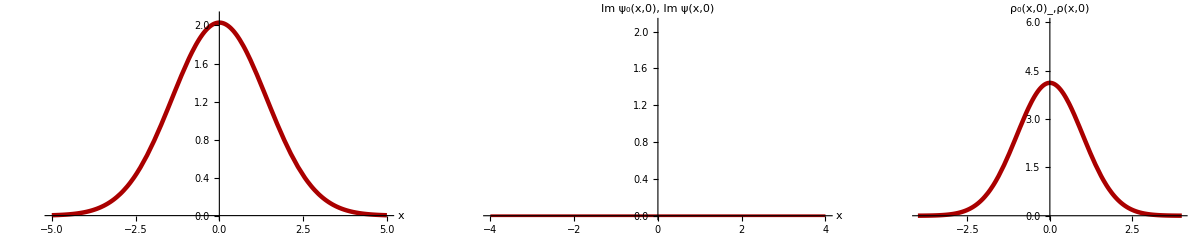

```mathematica
WWWA1=Plot[C1*Ref[x],{x,-5,5},AspectRatio->.4,PlotRange->{0,2.1},AxesLabel->{"x",""},PlotStyle->{Darker[Red],Thickness[.008]}];
WWWA2=Plot[C1*Imf[x],{x,-4,4},AspectRatio->.4,PlotRange->{0,2.1},AxesLabel->{"x","Im ψ_0(x,0), Im ψ(x,0)"},PlotStyle->{Darker[Red],Thickness[.005]}];
WWWA3=Plot[(C1*Ref[x])^2+(C1*Imf[x])^2,{x,-4,4},AspectRatio->.5,PlotRange->{0,6},AxesLabel->{"","ρ_0(x,0)_,ρ(x,0)"},PlotStyle->{Darker[Red],Thickness[.008]}];
GraphicsRow[{WWWA1,WWWA2,WWWA3},AspectRatio->.4]
```

```mathematica
Ref1[x_]:=0.0/;x<-s-b;
Ref1[x_]:=C1*Ref[x]/;-s-b≤x≤-s+b;
Ref1[x_]:=0.0/;-s+b<x<s-b;
Ref1[x_]:=C1*Ref[x]/;s-b<=x≤s+b;
Ref1[x_]:=0.0/;s+b<x;
```

```mathematica
Imf1[x_]:=0.0/;x<-s-b;
Imf1[x_]:=C1*Imf[x]/;-s-b≤x≤-s+b;
Imf1[x_]:=0.0/;-s+b<x<s-b;
Imf1[x_]:=C1*Imf[x]/;s-b<=x≤s+b;
Imf1[x_]:=0.0/;s+b<x;
```

```mathematica
∫_-4.0^4.0 Ref1[x]^2 ⅆx//N
```

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in x near {x} = {0.906126}. NIntegrate obtained 1.00457 and 0.011168 for the integral and error estimates.

1.00457

```mathematica
∫_-4.0^4.0 Imf1[x]^2 ⅆx//N
```

NIntegrate::izero: Integral and error estimates are 0 on all integration subregions. Try increasing the value of the MinRecursion option. If value of integral may be 0, specify a finite value for the AccuracyGoal option.

0.

```mathematica
(∫_-4.0^4.0 Ref1[x]^2 ⅆx+∫_-4.0^4.0 Imf1[x]^2 ⅆx)//N
```

NIntegrate::izero: Integral and error estimates are 0 on all integration subregions. Try increasing the value of the MinRecursion option. If value of integral may be 0, specify a finite value for the AccuracyGoal option.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in x near {x} = {0.906126}. NIntegrate obtained 1.00457 and 0.011168 for the integral and error estimates.

1.00457

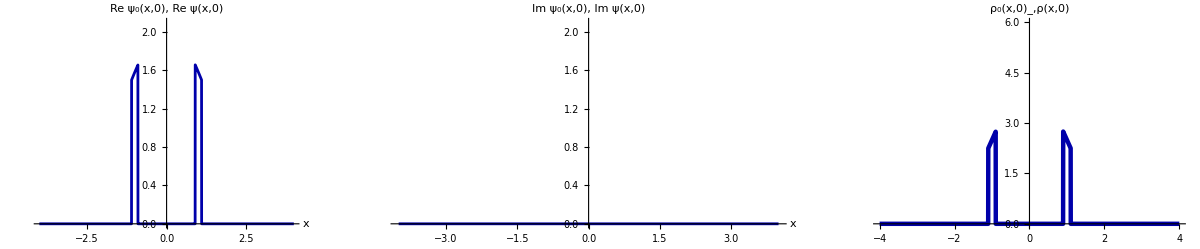

```mathematica
WWA1=Plot[Ref1[x],{x,-4,4},AxesOrigin->{0,0}AspectRatio->.4,PlotRange->{0,2.1},AxesLabel->{"x","Re ψ_0(x,0), Re ψ(x,0)"},PlotStyle->{Darker[Blue],Thickness[.005]}];
WWA2=Plot[Imf1[x],{x,-4,4},AspectRatio->.4,AxesOrigin->{0,0},PlotRange->{0,2.1},AxesLabel->{"x","Im ψ_0(x,0), Im ψ(x,0)"},PlotStyle->{Darker[Blue],Thickness[.005]}];
WWA3=Plot[Ref1[x]^2+Imf1[x]^2,{x,-4,4},AspectRatio->.5,PlotRange->{0,6},AxesOrigin->{0,0},AxesLabel->{"","ρ_0(x,0)_,ρ(x,0)"},PlotStyle->{Darker[Blue],Thickness[.008]}];
GraphicsRow[{WWA1,WWA2,WWA3},AspectRatio->.4,AxesOrigin->{0,0}]
```

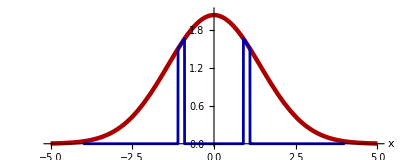

```mathematica
MMMA=Show[{WWWA1,WWA1},AspectRatio->.4]
```

```mathematica
WA=Plot[Ref1[x]^2,{x,-2,2},AspectRatio->.4,PlotRange->All,AxesLabel->{"x","Ref1[x]^2"},PlotStyle->{Black,Thickness[.005]},PlotLabel->"A"];
WB=Plot[Imf1[x]^2,{x,-2,2},AspectRatio->.4,PlotRange->All,AxesLabel->{"x","Imf1[x]^2"},PlotStyle->{Black,Thickness[.005]},PlotLabel->"B"];
WC=Plot[Ref1[x]^2+Imf1[x]^2,{x,-2,2},AspectRatio->.4,PlotRange->All,AxesLabel->{"x","Ref1[x]^2+Imf1[x]^2"},PlotStyle->{Black,Thickness[.005]},PlotLabel->"C"];
GraphicsRow[{WA,WB,Show[{WWWC,WC}]}]
```

Show::gcomb: Could not combine the graphics objects in Show[{WWWC,}].

FilterRules::rep: System`Private`SortOptions[$Failed] is not a valid replacement rule.

FilterRules::rep: FilterRules[System`Private`SortOptions[$Failed],{AlignmentPoint,AspectRatio,Axes,AxesLabel,AxesOrigin,AxesStyle,Background,BaselinePosition,BaseStyle,ColorOutput,«28»}] is not a valid replacement rule.

Lookup::invrl: The argument FilterRules[FilterRules[System`Private`SortOptions[$Failed],{AlignmentPoint,AspectRatio,Axes,AxesLabel,AxesOrigin,AxesStyle,Background,BaselinePosition,BaseStyle,ColorOutput,«28»}],{ImagePadding,ImageSize,AspectRatio}] is not a valid Association or a list of rules.

General::stop: Further output of Lookup::invrl will be suppressed during this calculation.

FilterRules::rep: System`Private`SortOptions[$Failed] is not a valid replacement rule.

General::stop: Further output of FilterRules::rep will be suppressed during this calculation.

Median::rectn: Rectangular array of real numbers is expected at position 1 in Median[{System`Dump`opts}].

Part::partd: Part specification {{Lookup[System`Dump`opts,System`Dump`name],Lookup[System`Dump`opts,System`Dump`name],{{Missing[NotAvailable],Missing[NotAvailable]},{Missing[NotAvailable],Missing[NotAvailable]}}}}⟦All,All,2,1⟧ is longer than depth of object.

DeleteMissing::invrp: The argument {{Lookup[System`Dump`opts,System`Dump`name],Lookup[System`Dump`opts,System`Dump`name],{{Missing[NotAvailable],Missing[NotAvailable]},{Missing[NotAvailable],Missing[NotAvailable]}}}}⟦All,All,2,1⟧ is not a valid Association or a list.

Part::partd: Part specification {{Lookup[System`Dump`opts,System`Dump`name],Lookup[System`Dump`opts,System`Dump`name],{{Missing[NotAvailable],Missing[NotAvailable]},{Missing[NotAvailable],Missing[NotAvailable]}}}}⟦All,All,2,2⟧ is longer than depth of object.

DeleteMissing::invrp: The argument {{Lookup[System`Dump`opts,System`Dump`name],Lookup[System`Dump`opts,System`Dump`name],{{Missing[NotAvailable],Missing[NotAvailable]},{Missing[NotAvailable],Missing[NotAvailable]}}}}⟦All,All,2,2⟧ is not a valid Association or a list.

Part::partd: Part specification {{Lookup[System`Dump`opts,System`Dump`name],Lookup[System`Dump`opts,System`Dump`name],{{Missing[NotAvailable],Missing[NotAvailable]},{Missing[NotAvailable],Missing[NotAvailable]}}}}⟦All,All,2,1⟧ is longer than depth of object.

General::stop: Further output of Part::partd will be suppressed during this calculation.

DeleteMissing::invrp: The argument {{Lookup[System`Dump`opts,System`Dump`name],Lookup[System`Dump`opts,System`Dump`name],{{Missing[NotAvailable],Missing[NotAvailable]},{Missing[NotAvailable],Missing[NotAvailable]}}}}⟦All,All,2,1⟧ is not a valid Association or a list.

General::stop: Further output of DeleteMissing::invrp will be suppressed during this calculation.

MapThread::mptd: Object Graphics`GraphicsGridDump`sizes$22431 at position {2, 1} in MapThread[Graphics`GraphicsGridDump`DividerCoordinates,{Graphics`GraphicsGridDump`sizes$22431,Graphics`GraphicsGridDump`ExpandOption[Spacings,Scaled[0.1],{2,4},Graphics`GraphicsGridDump`sizes$22431]}] has only 0 of required 1 dimensions.

MapThread::mptd: Object -Graphics`GraphicsGridDump`sizes$22431 at position {2, 1} in MapThread[Graphics`GraphicsGridDump`DividerCoordinates,{-Graphics`GraphicsGridDump`sizes$22431,-Graphics`GraphicsGridDump`ExpandOption[Spacings,Scaled[0.1],{2,4},Graphics`GraphicsGridDump`sizes$22431]}] has only 0 of required 1 dimensions.

MapThread::mptd: Object Min[-Graphics`GraphicsGridDump`sizes$22431,-Graphics`GraphicsGridDump`ExpandOption[Spacings,Scaled[0.1],{2,4},Graphics`GraphicsGridDump`sizes$22431]] at position {2, 1} in MapThread[{Graphics`GraphicsGridDump`DividerCoordinates,Graphics`GraphicsGridDump`DividerCoordinates},{Min[-Graphics`GraphicsGridDump`sizes$22431,-Graphics`GraphicsGridDump`ExpandOption[Spacings,Scaled[0.1],{2,4},Graphics`GraphicsGridDump`sizes$22431]],Max[-Graphics`GraphicsGridDump`sizes$22431,-Graphics`GraphicsGridDump`ExpandOption[Spacings,Scaled[0.1],{2,4},Graphics`GraphicsGridDump`sizes$22431]]}] has only 0 of required 1 dimensions.

General::stop: Further output of MapThread::mptd will be suppressed during this calculation.

-Graphics-

```mathematica
D1=2.0/s^2(4.0/π^3)^2
```

0.0332852

```mathematica
b*Pi
```

0.314159

```mathematica
t0=3.0;
```

```mathematica
L=8.0;
```

```mathematica
solution=NDSolve[
           {D[w[x,t], t]==D1*D[w[x,t], {x,2}]-k/(√2 a)*D[w[x,t], {x,1}],w[-L,t]==0,w[L,t]==0,
           w[x,0]==Ref1[x]^2.0+Imf1[x]^2.0},w,{x,-L,L},{t,0,t0},PrecisionGoal->∞]
```

NDSolve::mxsst: Using maximum number of grid points 10000 allowed by the MaxPoints or MinStepSize options for independent variable x.

{{w→InterpolatingFunction[{{-8., 8.}, {0., 3.}}, <>]}}

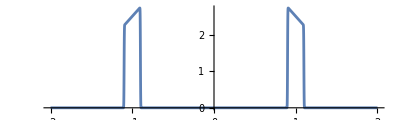

```mathematica
K0=Plot[Evaluate[w[x,0.0001]/.solution],{x,-2,2},PlotPoints->100,PlotRange->All,AspectRatio->.3]
```

```mathematica
tA=1.0/Pi
```

0.31831

```mathematica
solution=NDSolve[
           {D[w[x,t], t]==D1*D[w[x,t], {x,2}]-k/(√2 a)*D[w[x,t], {x,1}],w[-L,t]==0,w[L,t]==0,
           w[x,0]==Ref1[x]^2.0+Imf1[x]^2.0},w,{x,-L,L},{t,0,tA},PrecisionGoal->∞]
```

NDSolve::mxsst: Using maximum number of grid points 10000 allowed by the MaxPoints or MinStepSize options for independent variable x.

{{w→InterpolatingFunction[{{-8., 8.}, {0., 0.31831}}, <>]}}

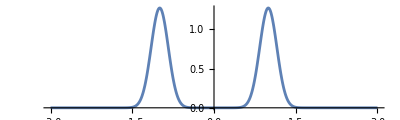

```mathematica
K00=Plot[Evaluate[w[x,tA]/.solution],{x,-3,3},PlotPoints->100,PlotRange->All,AspectRatio->.3]
```

```mathematica
Clear[z,n1,n,t,x,xmax,R,α,Rleft,Rright,F,z,zz]
R=s;
```

```mathematica
α=(2.0 s)/(4 b)^2
```

12.5

```mathematica
α/R
```

12.5

```mathematica
Clear[F,zz]
```

```mathematica
Rleft[R_,z_,t_][x_]:=z[x]+∑_(n=1)^40 t^n/(n!)(α/R)^n z[x+n*R]
Rright[R_,z_,t_][x_]:=z[x]+∑_(n=1)^40 t^n/(n!)(α/R)^n z[x-n*R]
```

```mathematica
F[R_,z_,t_][x_]:=ⅇ^(-(2α t)/R) Rleft[R,Rright[R,z,t],t][x];
```

```mathematica
zz[x_]:=Evaluate[w[xx,tA]/.solution/.xx->x][[1]]
```

InterpolatingFunction::dmval: Input value {-9.9998,0.31831} lies outside the range of data in the interpolating function. Extrapolation will be used.

InterpolatingFunction::dmval: Input value {-10.9998,0.31831} lies outside the range of data in the interpolating function. Extrapolation will be used.

InterpolatingFunction::dmval: Input value {-11.9998,0.31831} lies outside the range of data in the interpolating function. Extrapolation will be used.

General::stop: Further output of InterpolatingFunction::dmval will be suppressed during this calculation.

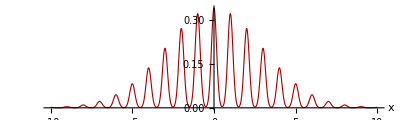

```mathematica
PA=Plot[F[R,zz,tA][x],{x,-10,10},PlotRange->All,PlotPoints->100,AspectRatio->.3,PlotStyle->{Thickness[.002],Darker[Red]},AxesLabel->{"x"," "}]
```

```mathematica
tB=2.0/Pi
```

0.63662

```mathematica
solution=NDSolve[
           {D[w[x,t], t]==D1*D[w[x,t], {x,2}]-k/(√2 a)*D[w[x,t], {x,1}],w[-L,t]==0,w[L,t]==0,
           w[x,0]==Ref1[x]^2.0+Imf1[x]^2.0},w,{x,-L,L},{t,0,tB},PrecisionGoal->∞]
```

NDSolve::mxsst: Using maximum number of grid points 10000 allowed by the MaxPoints or MinStepSize options for independent variable x.

{{w→InterpolatingFunction[{{-8., 8.}, {0., 0.63662}}, <>]}}

```mathematica
Rleft[R_,z_,t_][x_]:=z[x]+∑_(n=1)^35 t^n/(n!)(α/R)^n z[x+n*R]
Rright[R_,z_,t_][x_]:=z[x]+∑_(n=1)^35 t^n/(n!)(α/R)^n z[x-n*R]
```

```mathematica
F[R_,z_,t_][x_]:=ⅇ^(-(2α t)/R) Rleft[R,Rright[R,z,t],t][x];
```

```mathematica
zz[x_]:=Evaluate[w[xx,tB]/.solution/.xx->x][[1]]
```

InterpolatingFunction::dmval: Input value {-11.9998,0.63662} lies outside the range of data in the interpolating function. Extrapolation will be used.

InterpolatingFunction::dmval: Input value {-12.9998,0.63662} lies outside the range of data in the interpolating function. Extrapolation will be used.

InterpolatingFunction::dmval: Input value {-13.9998,0.63662} lies outside the range of data in the interpolating function. Extrapolation will be used.

General::stop: Further output of InterpolatingFunction::dmval will be suppressed during this calculation.

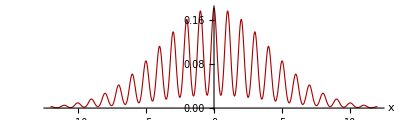

```mathematica
PB=Plot[F[R,zz,tB][x],{x,-12,12},PlotRange->All,PlotPoints->100,AspectRatio->.3,PlotStyle->{Thickness[.002],Darker[Red]},AxesLabel->{"x"," "}]
```

```mathematica
tC=4.0/Pi
```

1.27324

```mathematica
solution=NDSolve[
           {D[w[x,t], t]==D1*D[w[x,t], {x,2}]-k/(√2 a)*D[w[x,t], {x,1}],w[-L,t]==0,w[L,t]==0,
           w[x,0]==Ref1[x]^2.0+Imf1[x]^2.0},w,{x,-L,L},{t,0,tC},PrecisionGoal->∞]
```

NDSolve::mxsst: Using maximum number of grid points 10000 allowed by the MaxPoints or MinStepSize options for independent variable x.

{{w→InterpolatingFunction[{{-8., 8.}, {0., 1.27324}}, <>]}}

```mathematica
Rleft[R_,z_,t_][x_]:=z[x]+∑_(n=1)^40 t^n/(n!)(α/R)^n z[x+n*R]
Rright[R_,z_,t_][x_]:=z[x]+∑_(n=1)^40 t^n/(n!)(α/R)^n z[x-n*R]
```

```mathematica
F[R_,z_,t_][x_]:=ⅇ^(-(2α t)/R) Rleft[R,Rright[R,z,t],t][x];
```

```mathematica
zz[x_]:=Evaluate[w[xx,tC]/.solution/.xx->x][[1]]
```

InterpolatingFunction::dmval: Input value {-14.9997,1.27324} lies outside the range of data in the interpolating function. Extrapolation will be used.

InterpolatingFunction::dmval: Input value {-15.9997,1.27324} lies outside the range of data in the interpolating function. Extrapolation will be used.

InterpolatingFunction::dmval: Input value {-16.9997,1.27324} lies outside the range of data in the interpolating function. Extrapolation will be used.

General::stop: Further output of InterpolatingFunction::dmval will be suppressed during this calculation.

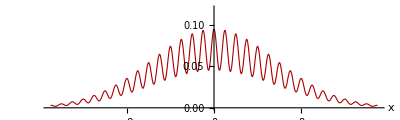

```mathematica
PC=Plot[F[R,zz,tC][x],{x,-15,15},PlotRange->{0,.12},PlotPoints->100,AspectRatio->.3,PlotStyle->{Thickness[.002],Darker[Red]},AxesLabel->{"x"," "}]
```

```mathematica
tD=6.0/Pi
```

1.90986

```mathematica
solution=NDSolve[
           {D[w[x,t], t]==D1*D[w[x,t], {x,2}]-k/(√2 a)*D[w[x,t], {x,1}],w[-L,t]==0,w[L,t]==0,
           w[x,0]==Ref1[x]^2.0+Imf1[x]^2.0},w,{x,-L,L},{t,0,tD},PrecisionGoal->∞]
```

NDSolve::mxsst: Using maximum number of grid points 10000 allowed by the MaxPoints or MinStepSize options for independent variable x.

{{w→InterpolatingFunction[{{-8., 8.}, {0., 1.90986}}, <>]}}

```mathematica
Rleft[R_,z_,t_][x_]:=z[x]+∑_(n=1)^45 t^n/(n!)(α/R)^n z[x+n*R]
Rright[R_,z_,t_][x_]:=z[x]+∑_(n=1)^45 t^n/(n!)(α/R)^n z[x-n*R]
```

```mathematica
F[R_,z_,t_][x_]:=ⅇ^(-(2α t)/R) Rleft[R,Rright[R,z,t],t][x];
```

```mathematica
zz[x_]:=Evaluate[w[xx,tD]/.solution/.xx->x][[1]]
```

InterpolatingFunction::dmval: Input value {-19.9996,1.90986} lies outside the range of data in the interpolating function. Extrapolation will be used.

InterpolatingFunction::dmval: Input value {-20.9996,1.90986} lies outside the range of data in the interpolating function. Extrapolation will be used.

InterpolatingFunction::dmval: Input value {-21.9996,1.90986} lies outside the range of data in the interpolating function. Extrapolation will be used.

General::stop: Further output of InterpolatingFunction::dmval will be suppressed during this calculation.

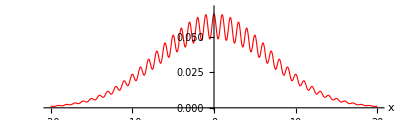

```mathematica
PD=Plot[F[R,zz,tD][x],{x,-20,20},PlotRange->{0,.07},PlotPoints->100,AspectRatio->.3,PlotStyle->{Thickness[.002],Red},AxesLabel->{"x"," "}]
```

```mathematica
LLL1=Show[Graphics[Line[{{-20,0},{20,0}}]]];
```

```mathematica
Gauss[x_,aa_]:=(ⅇ^(-x^2/(2 aa)))/(√(2 π aa))
```

```mathematica
A3=Plot[Gauss[x,2(D1+α)tA],{x,-10,10},AspectRatio->.3,PlotRange->All,PlotStyle->{Thickness[.003],Darker[Green]},AxesOrigin->{0,0},PlotLabel->"A"];
```

```mathematica
B3=Plot[Gauss[x,2(D1+α)tB],{x,-12,12},AspectRatio->.3,PlotRange->All,PlotStyle->{Thickness[.003],Darker[Green]},AxesOrigin->{0,0},PlotLabel->"B"];
```

```mathematica
C3=Plot[Gauss[x,2(D1+α)tC],{x,-15,15},AspectRatio->.3,PlotRange->All,PlotStyle->{Thickness[.003],Darker[Green]},AxesOrigin->{0,0},PlotLabel->"C"];
```

```mathematica
D3=Plot[1.0 Gauss[x,2(D1+α)tD],{x,-20,20},AspectRatio->.3,PlotRange->All,PlotStyle->{Thickness[.003],Darker[Green]},AxesOrigin->{0,0},PlotLabel->"D"];
```

```mathematica
KA=Show[{A3,PA}];
```

```mathematica
KB=Show[{B3,PB}];
```

```mathematica
KC=Show[{C3,PC}];
```

```mathematica
KD=Show[{D3,PD}];
```

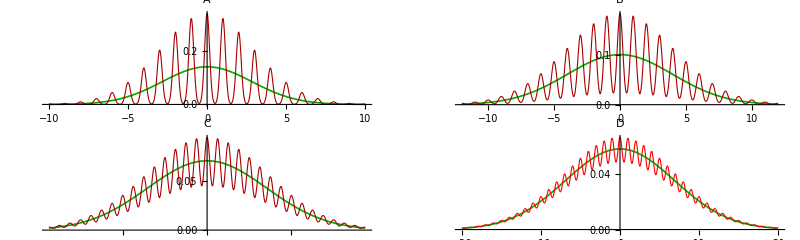

```mathematica
GraphicsGrid[{{KA,KB},{KC,KD}},AspectRatio->.4]
```

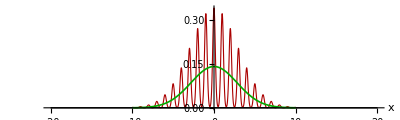
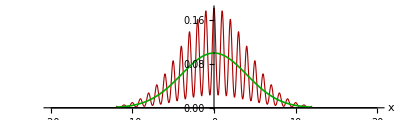
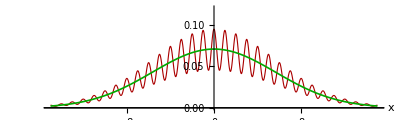
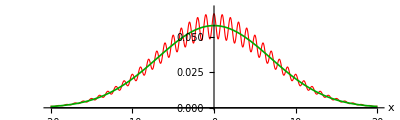
StackGraphics[{-Graphics-,-Graphics-,-Graphics-,-Graphics-},ViewPoint→{4,-5,3},AspectRatio→0.6,Epilog→{Inset[A: t = 1.0/π,Scaled[{0.5,0.09}]],Inset[B: t = 2.0/π,Scaled[{0.67,0.17}]],Inset[C: t = 4.0/π,Scaled[{0.8,0.26}]],Inset[D: t = 6.0/π,Scaled[{0.92,0.35}]]}]

```mathematica
StackGraphics[{Show[{PA,LLL1,A3}],Show[{PB,LLL1,B3}],Show[{PC,LLL1,C3}],Show[{PD,LLL1,D3}]},ViewPoint->{4,-5,3},AspectRatio->.6,Epilog->{
Inset["A: t = 1.0/π",Scaled[{.5,.09}]],
Inset["B: t = 2.0/π",Scaled[{.67,.17}]],
Inset["C: t = 4.0/π",Scaled[{.8,.26}]],
Inset["D: t = 6.0/π",Scaled[{.92,.35}]]}]
```